```mathematica
sdUrl:=TemplateApply["http://www.spacedock.info/api/browse?page=`p`&count=`c`",<|"p"->page,"c"->100|>];
```

```mathematica
sdUrl[2]
```

http://www.spacedock.info/api/browse?page=1&count=100[2]

```mathematica
page=6;sdUrl
```

http://www.spacedock.info/api/browse?page=6&count=100

```mathematica
name=ver={}
Do[sdUrl:=TemplateApply["http://www.spacedock.info/api/browse?page=`p`&count=`c`",<|"p"->page,"c"->2|>];raw=URLExecute[sdUrl,"RawJSON"];
name=Flatten[{name,raw[["result",All,"name"]]}];
ver=Flatten[{ver,raw[["result",All,"versions",1,"game_version"]]}];
,{page,1,4}]
```

{}

```mathematica
name
```

{Persistent Trails Continued...,Semiotic Standard for Kerbal Vessels,BDArmory Weapons Extension,Kerbin-SideJobs (Contracts Pack),Em Drive,CTTStockRebalance,Kerbalism Simplified,Deltaglider XR-1 For KSP}

```mathematica
ver
```

{1.4.1,1.4.3,1.3.1,1.1.2,1.2.2,1.3.0,1.2.2,1.0.5}

```mathematica
sdUrl:=TemplateApply["http://www.spacedock.info/api/browse?page=`p`&count=`c`",<|"p"->1,"c"->1|>];raw=URLExecute[sdUrl];
```

```mathematica
raw
```

{pages→1560,count→1,result→{{name→Persistent Trails Continued...,short_description→Document your epic journeys! Fly in formation! Race your friends! Paint the skies!,default_version_id→8217,author→Jplrepo,donations→https://www.patreon.com/JPLRepo,game→Kerbal Space Program,shared_authors→{},website→http://forum.kerbalspaceprogram.com/index.php?/topic/161454-13,followers→28,downloads→966,id→1398,game_id→3102,background→/content/Jplrepo_405/Persistent_Trails_Continued/Persistent_Trails_Continued-1496400853.8806963.png,versions→{{friendly_version→V1.7,download_path→/mod/1398/Persistent%20Trails%20Continued.../download/V1.7,game_version→1.4.1,id→8217,changelog→Fix and Re-compile for KSP 1.4.1},{friendly_version→V1.6,download_path→/mod/1398/Persistent%20Trails%20Continued.../download/V1.6,game_version→1.3.1,id→6962,changelog→Re-compile for KSP 1.3.1},{friendly_version→V1.5,download_path→/mod/1398/Persistent%20Trails%20Continued.../download/V1.5,game_version→1.3.0,id→6050,changelog→Changes and re-compiled for KSP 1.3   \r
Fixed lights and Antennas so they don't deploy for ghost vessels.   \r
Added 3 decimal point precision on distance readout in GUI.}},url→/mod/1398/Persistent%20Trails%20Continued...,bg_offset_y→Null,source_code→https://github.com/JPLRepo/KSPPersistentTrails,license→MIT}},page→1}

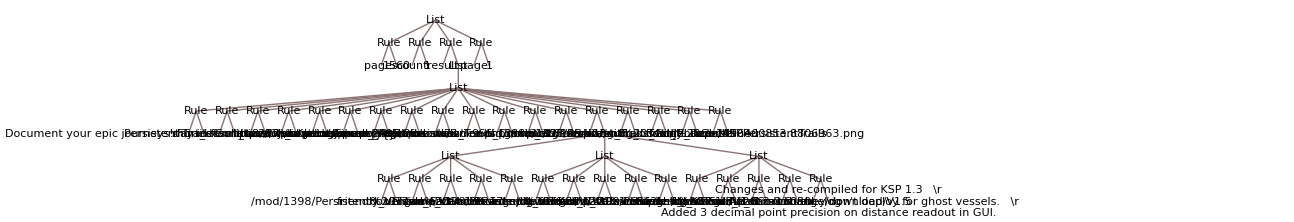

```mathematica
TreeForm[raw]
```

```mathematica
Remove[a[[2]]]
```

Remove::ssym: a⟦2⟧ 不是一个符号.